```mathematica
Subscript[m, K]=493.6;Subscript[m, μ]=105.6
```

105.6

```mathematica
Subscript[m, K]
```

493.6

```mathematica
Subscript[γ, μ]:=(1-Subscript[β, μ]^2)^(-1/2)
```

```mathematica
Subscript[p, μ']:=Subscript[γ, μ] Subscript[m, μ] Subscript[β, μ]
```

```mathematica
Solve[Subscript[γ, μ] Subscript[m, μ] (1+Subscript[β, μ])==Subscript[m, K],Subscript[β, μ]]
```

{{β_μ→0.912467}}

```mathematica
(105.6 Subscript[β, μ])/(√(1-Subscript[β, μ]^2))/.{{Subscript[β, μ]->0.9124670633714549}}
```

{235.504}

```mathematica
First[{235.50405186385743}]
```

```mathematica
Subscript[p, μ']=235.50405186385743
```

235.504

```mathematica
Subscript[β, μ]/.{{Subscript[β, μ]->0.9124670633714549}}
```

{0.912467}

```mathematica
First[{0.9124670633714549}]
```

```mathematica
Subscript[p, μ']=0.9124670633714549
```

0.912467

```mathematica
Subscript[p, μ']
```

(105.6 β_μ)/(√(1-β_μ^2))

```mathematica
Subscript[Ε, K]=1400;γ=2.8363;β=0.935785
```

0.935785

```mathematica
Subscript[Ε, ν']=Subscript[m, K]-Subscript[Ε, μ'];Subscript[Ε, μ']=Subscript[p, μ']
```

235.504

```mathematica
Subscript[Ε, μ']
```

235.504

```mathematica
Subscript[Ε, ν']
```

258.096

```mathematica
Subscript[p, K]=Subscript[Ε, K] β
```

1310.1

```mathematica
β;γ
```

2.8363

```mathematica
Subscript[p, ν']=-Subscript[p, μ']
```

-235.504

```mathematica
NSolve[{Subscript[Ε, K]==Subscript[Ε, μ]+Subscript[Ε, ν],Subscript[Ε, ν]^2-Subscript[p, ν]^2==Subscript[Ε, ν']^2-Subscript[p, ν']^2,Subscript[Ε, μ]^2-Subscript[p, μ]^2==Subscript[Ε, μ']^2-Subscript[p, μ']^2,Subscript[p, μ]^2==Subscript[p, K]^2+Subscript[p, ν]^2-2 Subscript[p, K] Subscript[p, ν] Cos[θ]},{Subscript[Ε, μ],Subscript[Ε, ν],Subscript[p, ν],Subscript[p, μ]},Reals]
```

NSolve::ratnz: NSolve 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

{{Ε_μ→ConditionalExpression[(2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)),-1.06862<Cos[θ]<-0.54221||Cos[θ]<-1.06862],Ε_ν→ConditionalExpression[1400.-1. ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2))),-1.06862<Cos[θ]<-0.54221||Cos[θ]<-1.06862],p_ν→ConditionalExpression[-0.0000230466 √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2),-1.06862<Cos[θ]<-0.54221||Cos[θ]<-1.06862],p_μ→ConditionalExpression[-0.000193497 √(4.58414×10^13+1.61284×10^6 Cos[θ] √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)+0.0141861 (3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)),-1.06862<Cos[θ]<-0.54221||Cos[θ]<-1.06862]},{Ε_μ→ConditionalExpression[(2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)),-1.06862<Cos[θ]<-0.54221||Cos[θ]<-1.06862],Ε_ν→ConditionalExpression[1400.-1. ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2))),-1.06862<Cos[θ]<-0.54221||Cos[θ]<-1.06862],p_ν→ConditionalExpression[-0.0000230466 √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2),-1.06862<Cos[θ]<-0.54221||Cos[θ]<-1.06862],p_μ→ConditionalExpression[0.000193497 √(4.58414×10^13+1.61284×10^6 Cos[θ] √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)+0.0141861 (3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)),-1.06862<Cos[θ]<-0.54221||Cos[θ]<-1.06862]},{Ε_μ→ConditionalExpression[(2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)),0.54221<Cos[θ]<1.06862||Cos[θ]>1.06862],Ε_ν→ConditionalExpression[1400.-1. ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2))),0.54221<Cos[θ]<1.06862||Cos[θ]>1.06862],p_ν→ConditionalExpression[0.0000230466 √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2),0.54221<Cos[θ]<1.06862||Cos[θ]>1.06862],p_μ→ConditionalExpression[-0.000193497 √(4.58414×10^13-1.61284×10^6 Cos[θ] √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)+0.0141861 (3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)),0.54221<Cos[θ]<1.06862||Cos[θ]>1.06862]},{Ε_μ→ConditionalExpression[(2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)),0.54221<Cos[θ]<1.06862||Cos[θ]>1.06862],Ε_ν→ConditionalExpression[1400.-1. ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2))),0.54221<Cos[θ]<1.06862||Cos[θ]>1.06862],p_ν→ConditionalExpression[0.0000230466 √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2),0.54221<Cos[θ]<1.06862||Cos[θ]>1.06862],p_μ→ConditionalExpression[0.000193497 √(4.58414×10^13-1.61284×10^6 Cos[θ] √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)+0.0141861 (3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)-2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)),0.54221<Cos[θ]<1.06862||Cos[θ]>1.06862]},{Ε_μ→ConditionalExpression[(2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)),-1.06862<Cos[θ]<-0.54221||Cos[θ]>1.06862],Ε_ν→ConditionalExpression[1400.-1. ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2))),-1.06862<Cos[θ]<-0.54221||Cos[θ]>1.06862],p_ν→ConditionalExpression[-0.0000230466 √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2),-1.06862<Cos[θ]<-0.54221||Cos[θ]>1.06862],p_μ→ConditionalExpression[-0.000193497 √(4.58414×10^13+1.61284×10^6 Cos[θ] √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)+0.0141861 (3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)),-1.06862<Cos[θ]<-0.54221||Cos[θ]>1.06862]},{Ε_μ→ConditionalExpression[(2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)),-1.06862<Cos[θ]<-0.54221||Cos[θ]>1.06862],Ε_ν→ConditionalExpression[1400.-1. ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2))),-1.06862<Cos[θ]<-0.54221||Cos[θ]>1.06862],p_ν→ConditionalExpression[-0.0000230466 √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2),-1.06862<Cos[θ]<-0.54221||Cos[θ]>1.06862],p_μ→ConditionalExpression[0.000193497 √(4.58414×10^13+1.61284×10^6 Cos[θ] √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)+0.0141861 (3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)),-1.06862<Cos[θ]<-0.54221||Cos[θ]>1.06862]},{Ε_μ→ConditionalExpression[(2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)),0.54221<Cos[θ]<1.06862||Cos[θ]<-1.06862],Ε_ν→ConditionalExpression[1400.-1. ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2))),0.54221<Cos[θ]<1.06862||Cos[θ]<-1.06862],p_ν→ConditionalExpression[0.0000230466 √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2),0.54221<Cos[θ]<1.06862||Cos[θ]<-1.06862],p_μ→ConditionalExpression[-0.000193497 √(4.58414×10^13-1.61284×10^6 Cos[θ] √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)+0.0141861 (3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)),0.54221<Cos[θ]<1.06862||Cos[θ]<-1.06862]},{Ε_μ→ConditionalExpression[(2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)),0.54221<Cos[θ]<1.06862||Cos[θ]<-1.06862],Ε_ν→ConditionalExpression[1400.-1. ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2))),0.54221<Cos[θ]<1.06862||Cos[θ]<-1.06862],p_ν→ConditionalExpression[0.0000230466 √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2),0.54221<Cos[θ]<1.06862||Cos[θ]<-1.06862],p_μ→ConditionalExpression[0.000193497 √(4.58414×10^13-1.61284×10^6 Cos[θ] √(3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)+0.0141861 (3.66915×10^15-5.27163×10^12 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))+1.88273×10^9 ((2.84096×10^-13 (-1.84304×10^26+1.72613×10^26 Cos[θ]^2))/(-4.×10^10+3.50277×10^10 Cos[θ]^2)+2.65853×10^-10 √((-5.69121×10^43 Cos[θ]^2+1.93584×10^44 Cos[θ]^4)/((-4.×10^10+3.50277×10^10 Cos[θ]^2)^2)))^2)),0.54221<Cos[θ]<1.06862||Cos[θ]<-1.06862]}}

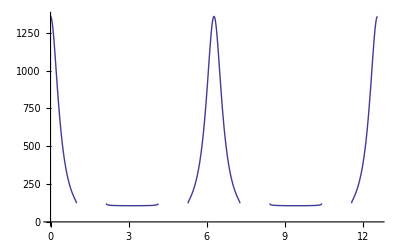

```mathematica
Plot[7.102405950556593*^-18 (1.2812155887371872*^19-(4.487808992017322*^29 Cos[θ]^2)/(-4.*^10+3.5027742649*^10 Cos[θ]^2)-(3.74314*^7 Cos[θ] √(-5.691206560709312*^43+1.9358380068889443*^44 Cos[θ]^2))/(-4.*^10+3.5027742649*^10 Cos[θ]^2)),{θ,0,4π}]
```

```mathematica
Minimize[{7.102405950556593*^-18 (1.2812155887371872*^19-(4.487808992017322*^29 Cos[θ]^2)/(-4.*^10+3.5027742649*^10 Cos[θ]^2)-(3.74314*^7 Cos[θ] √(-5.691206560709312*^43+1.9358380068889443*^44 Cos[θ]^2))/(-4.*^10+3.5027742649*^10 Cos[θ]^2)),θ<3.5,θ>2.5},θ]
```

{106.971,{θ→3.14159}}

```mathematica
Minimize[7.102405950556593*^-18 (1.2812155887371872*^19-(4.487808992017322*^29 Cos[θ]^2)/(-4.*^10+3.5027742649*^10 Cos[θ]^2)-(3.74314*^7 Cos[θ] √(-5.691206560709312*^43+1.9358380068889443*^44 Cos[θ]^2))/(-4.*^10+3.5027742649*^10 Cos[θ]^2)),θ]
```

NMinimize::nrnum: 函数值 4.05432×10^18 + 1.25377×10^18\ ⅈ 不是位于 {θ} = {-1.01934} 的一个实数.

{138.216,{θ→-0.969346}}

```mathematica
7.102405950556593*^-18 (1.2812155887371872*^19-(4.487808992017322*^29 Cos[θ]^2)/(-4.*^10+3.5027742649*^10 Cos[θ]^2)-(3.74314*^7 Cos[θ] √(-5.691206560709312*^43+1.9358380068889443*^44 Cos[θ]^2))/(-4.*^10+3.5027742649*^10 Cos[θ]^2))/.θ->(π-0.01)
```

106.971

```mathematica
Precision[106.97088645162754]
```

MachinePrecision

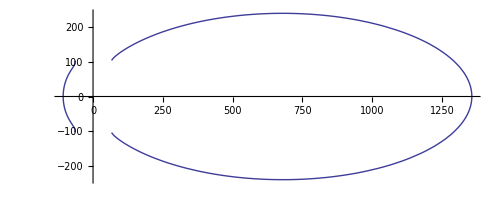

```mathematica
PolarPlot[7.102405950556593*^-18 (1.2812155887371872*^19-(4.487808992017322*^29 Cos[θ]^2)/(-4.*^10+3.5027742649*^10 Cos[θ]^2)-(3.74314*^7 Cos[θ] √(-5.691206560709312*^43+1.9358380068889443*^44 Cos[θ]^2))/(-4.*^10+3.5027742649*^10 Cos[θ]^2)),{θ,0,2π}]
```

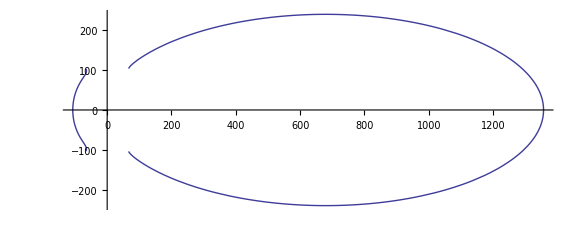

```mathematica
Show[%57,ImageSize->Large]
```